```mathematica
(* T A S K 1 *)
years  = {1971, 1972, 1974, 1978, 1982, 1985, 1989, 1993, 1997, 1999, 2000}
```

{1971,1972,1974,1978,1982,1985,1989,1993,1997,1999,2000}

```mathematica
trans = {2.25, 2.5, 5, 29, 120, 275, 1180, 3100, 7500, 24000, 42000}
```

{2.25,2.5,5,29,120,275,1180,3100,7500,24000,42000}

```mathematica
f[x_] := c + b*x
```

```mathematica
Err[c_, b_] := Sum[(f[years[[i]]] - Log[trans[[i]]])^2,{i,1,Length[years]}]
```

```mathematica
Err[c, b]
```

(-0.81093+1971 b+c)^2+(-0.916291+1972 b+c)^2+(1974 b+c-Log[5])^2+(1978 b+c-Log[29])^2+(1982 b+c-Log[120])^2+(1985 b+c-Log[275])^2+(1989 b+c-Log[1180])^2+(1993 b+c-Log[3100])^2+(1997 b+c-Log[7500])^2+(1999 b+c-Log[24000])^2+(2000 b+c-Log[42000])^2

```mathematica
sol = Solve[{D[Err[c,b], c] ==  0, D[Err[c,b], b] == 0}, {c, b}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{43680.,22.,-123.749},{8.6727×10^7,43680.,-246485.}} may contain significant numerical errors.

{{c→-652.777,b→0.331613}}

```mathematica
g[x_] =f[x] /.sol[[1]]
```

-652.777+0.331613 x

```mathematica
t[x_] = E^sol[[1,1,2]] *E^(sol[[1,2,2]]*x)
```

3.18017×10^-284 ⅇ^(0.331613 x)

```mathematica
ⅇ^(x (b->0.3316128250238776)+(c->-652.7772328705887))
```

ⅇ^(x (b→0.331613)+(c→-652.777))

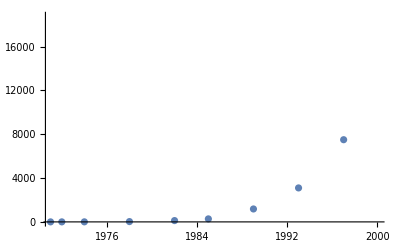

```mathematica
points = ListPlot[Transpose[{years, trans}]]
```

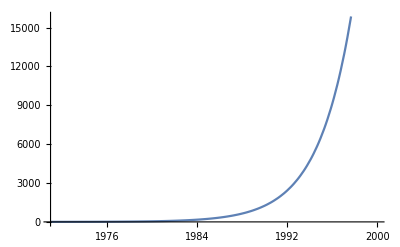

```mathematica
line = Plot[t[x], {x,1971, 2000}]
```

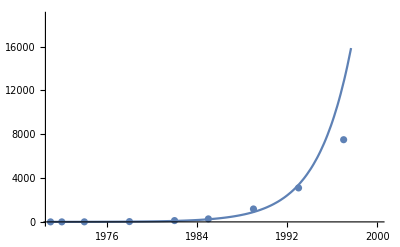

```mathematica
Show[points, line]
```

```mathematica
(* T A S K 1 *)
```

```mathematica
(* T A S K 2 *)

A := {{5, 10}, {10, 30}}
```

```mathematica
B:={{8}, {20}}
```

```mathematica
LinearSolve[A, B]
```

{{4/5},{2/5}}

```mathematica
a = Inverse[A].B
```

{{4/5},{2/5}}

```mathematica
d[x_] = a[[1, 1]] + a[[2, 1]]*x
```

4/5+(2 x)/5

```mathematica
valuesX := {0, 1, 2, 3, 4}
```

```mathematica
valuesY := {1, 2, 1, 0, 4}
```

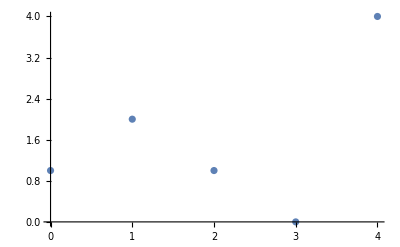

```mathematica
pl1 = ListPlot[Transpose[{valuesX, valuesY}]]
```

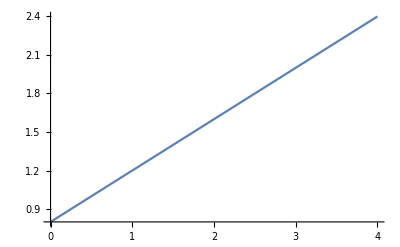

```mathematica
pl2 = Plot[f[x], {x, 0, 4}]
```

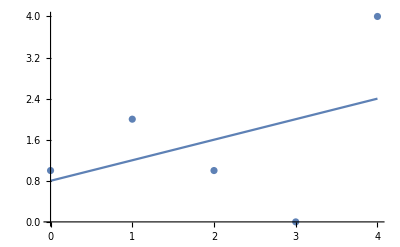

```mathematica
Show[pl1, pl2]
```